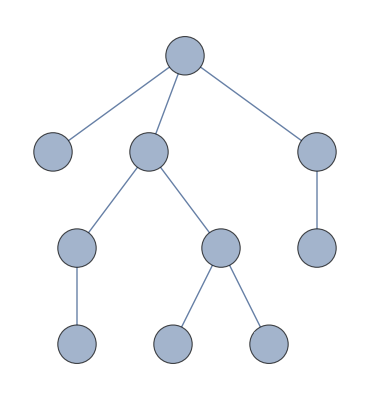

```mathematica
e ={1->2,1->3,1->4,3->5,3->6,5->8,6->9,4->7,6->10};
root=1;
g= Graph[e, GraphLayout->{"LayeredEmbedding","RootVertex"->root},VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

## Лабораторная 4.

```mathematica
Is=10;
ug=UndirectedGraph[g];
pred=ConstantArray[0,Is];(*список предков*)
depth=ConstantArray[0,Is]; (*список глубин узлов*)
dinast=ConstantArray[0,Is];(*династичесий обход*)
posl={};                                            (*последовательность обхода*)
DepthFirstScan[ug,root,{"FrontierEdge"->Function[edge,{
pred[[edge[[2]]]]=edge[[1]],
depth[[edge[[2]]]]=depth[[edge[[1]]]] + 1
}],
"PrevisitVertex"->Function[vertex,{If[posl≠{},dinast[[posl[[-1]]]]=vertex],AppendTo[posl,vertex]}]
}];
dinast[[posl[[-1]]]]=root;
(*Print[Range[Is]];
Print[pred];
Print[depth];
Print[dir];
Print[dinast];
Print[posl];*)
```

```mathematica
(*5. Списковые структуры вывести в виде таблицы (список связи или династического обхода можно не встраивать в таблицу,а вывести отдельным списком).*)
Grid[{Prepend[Range[Is],"i"],Prepend[pred,"pred[i]"],Prepend[depth,"depth[i]"],Prepend[dinast,"dinast[i]"]},Frame->All,ItemStyle->{{Bold},{Bold}}]
Print[posl]
```

i | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
pred[i] | 0 | 1 | 1 | 1 | 3 | 3 | 4 | 5 | 6 | 6
depth[i] | 0 | 1 | 1 | 1 | 2 | 2 | 2 | 3 | 3 | 3
dinast[i] | 2 | 3 | 5 | 7 | 8 | 9 | 1 | 6 | 10 | 4

{1,2,3,5,8,6,9,10,4,7}

## Лабораторная 4. Дополнительное задание.

```mathematica
(* Определение единственной цепи в дереве. *)
f1[x1_]:=Block[{u1},
u1=NestWhileList[pred[[#]]&,x1,pred[[#]]≠0&]
];
f1[10]
f1[7]
f1[5]

(*While[pred[[i]]≠0,Print[pred[[i]]];i=pred[[i]]]*)
```

{10,6,3,1}

{7,4,1}

{5,3,1}

```mathematica
(* Определение длины пути между двумя любыми вершинами дерева (плюс сам путь).*)
f2[x2_,y2_]:=Block[{ux,uy,h1,h2,x,y},
x=x2;
y=y2;
h1=depth[[x2]];
h2=depth[[y2]];
ux={x};
uy={y};
While[h1≠h2,If[h1>h2,{x=pred[[x]],h1=h1-1,AppendTo[ux,x]},{y=pred[[y]],h2=h2-1,PrependTo[uy,y]}]];
While[x≠y,{x=pred[[x]],AppendTo[ux,x],y=pred[[y]],PrependTo[uy,y]}];
ux=Flatten[Append[ux,Drop[uy,1]]];
List[Length[ux]-1,ux]
];
f2[9,5]
f2[3,10]
f2[10,10]
```

{3,{9,6,3,5}}

{2,{3,6,10}}

{0,{10}}

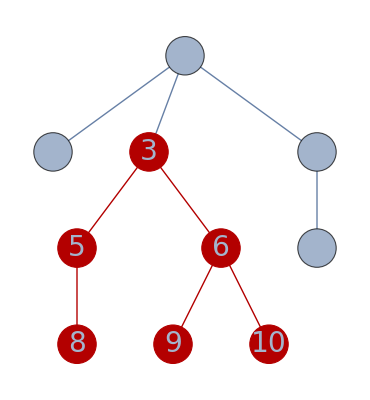

{1,2,3,5,8,6,9,10,4,7}

{8}

```mathematica
(* Нахождение поддерева с корнем в заданном узле.*)
f3[k_]:=Block[{d,i,n,u},
d=depth[[k]];
i=dinast[[k]];
n=1;
u=NestWhileList[dinast[[#]]&,i,depth[[#]]>d&];
PrependTo[u,k];
Drop[u,-1]
];
HighlightGraph[g,Subgraph[g,f3[3]]]
f3[1]
f3[8]
```

```mathematica
(* Определение всех листьев дерева (первый вариант).*)
f4[r_]:=Block[{i,l},
i=dinast[[r]];
l={};
While[i≠r,{If[depth[[i]]≥depth[[dinast[[i]]]],AppendTo[l,i]],i=dinast[[i]]}];
Return[l]
];
f4[root]
```

{2,8,9,10,7}

```mathematica
(* Определение всех листьев дерева (второй вариант).*)
f5[r_]:=Block[{i,l},
i=dinast[[r]];
l={};
While[i≠r,{If[i≠pred[[dinast[[i]]]],AppendTo[l,i]],i=dinast[[i]]}];
Return[l]
];
f5[root]
```

{2,8,9,10,7}